```mathematica
f2[t_]:=Piecewise[{{t,0≤t<1},{2-t,1≤ t<2}}]
```

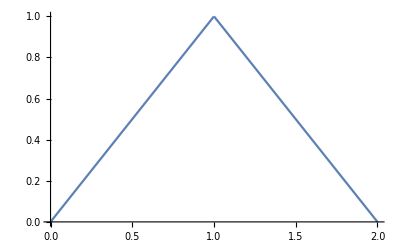

```mathematica
Plot[f2[t],{t,0,2}]
```

```mathematica
Integrate[t Exp[-p t],t]
```

-(ⅇ^(-p t) (1+p t))/p^2

```mathematica
Integrate[t Exp[-p t],{t,0,1}]
```

(1-ⅇ^-p (1+p))/p^2

```mathematica
Integrate[2Exp[-p t],{t,1,2}]
```

(2 ⅇ^(-2 p) (-1+ⅇ^p))/p

```mathematica
Integrate[t Exp[-p t],{t,1,2}]
```

(ⅇ^(-2 p) (-1-2 p+ⅇ^p (1+p)))/p^2

```mathematica
Simplify[(1-ⅇ^-p (1+p))/p^2 + (2 ⅇ^(-2 p) (-1+ⅇ^p))/p-(ⅇ^(-2 p) (-1-2 p+ⅇ^p (1+p)))/p^2]
```

(ⅇ^(-2 p) (-1+ⅇ^p)^2)/p^2

```mathematica
1/(1-Exp[-p 2])Simplify[Integrate[t Exp[-p t],{t,0,1}]+Integrate[(2-t) Exp[-p t],{t,1,2}]]
```

(ⅇ^(-2 p) (-1+ⅇ^p)^2)/((1-ⅇ^(-2 p)) p^2)

### Pregunta 3

```mathematica
InverseLaplaceTransform[(p(p+2))/(p^2+2p+5),p,t]
```

5/4 ⅈ ⅇ^((-1-2 ⅈ) t) (-1+ⅇ^(4 ⅈ t))+DiracDelta[t]

```mathematica
InverseLaplaceTransform[-5/(p^2+2p+5),p,t]
```

5/4 ⅈ ⅇ^((-1-2 ⅈ) t) (-1+ⅇ^(4 ⅈ t))

```mathematica
FullSimplify[5/4 ⅈ ⅇ^((-1-2 ⅈ) t) (-1+ⅇ^(4 ⅈ t))]
```

5 Cos[t] Sin[t] (-Cosh[t]+Sinh[t])

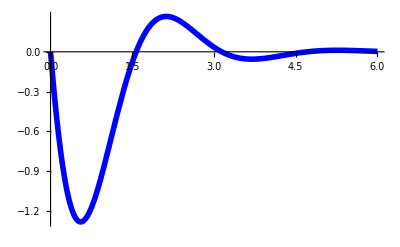

```mathematica
plot3a =Plot[5 Cos[t] Sin[t] (-Cosh[t]+Sinh[t]),{t,0,6},PlotRange->All,PlotStyle->{Blue,Thickness[0.01]}]
```

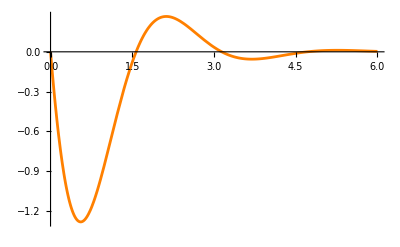

```mathematica
plot3b =Plot[-5/2 Exp[-t]Sin[2t],{t,0,6},PlotStyle->{Orange,Thickness[0.005]}]
```

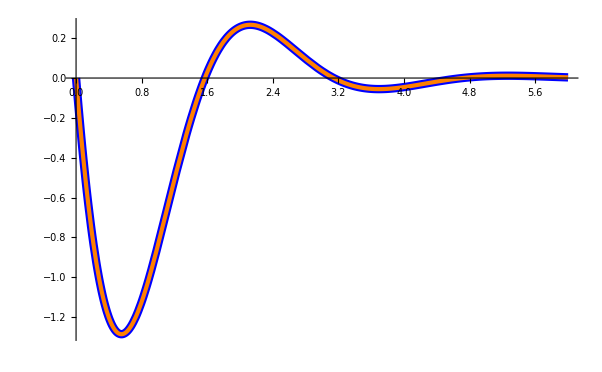

```mathematica
Show[plot3a,plot3b] (*Es la misma funcion*)
```

### Pregunta 4

```mathematica
(*Comparando la ecuacion obtenida por el mathematica y la mia en un grafico*)
```

```mathematica
Clear[q]
```

```mathematica
DSolve[{q''[t]+300 q'[t]+20000q[t]==200Sin[100 t], q[0]==0,q'[0]==0},q[t],t]
```

{{q[t]→-1/500 ⅇ^(-200 t) (2-5 ⅇ^(100 t)+3 ⅇ^(200 t) Cos[100 t]-ⅇ^(200 t) Sin[100 t])}}

```mathematica
q[t_]:=-1/500 ⅇ^(-200 t) (2-5 ⅇ^(100 t)+3 ⅇ^(200 t) Cos[100 t]-ⅇ^(200 t) Sin[100 t]);
```

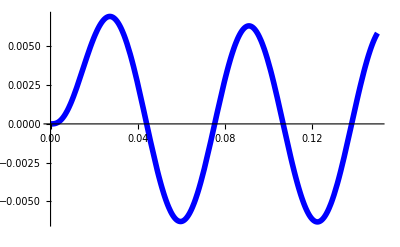

```mathematica
plot4a = Plot[q[t],{t,0,0.15},PlotStyle->{Blue,Thickness[0.01]}]
```

```mathematica
(*Nuestra Solucion*)
```

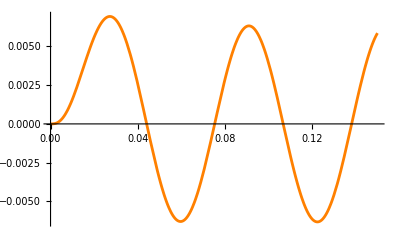

```mathematica
plot4b =Plot[1/500 Sin[100 t]-3/500 Cos[100t]+Exp[-100 t]/100-Exp[-200 t]/250,{t,0,0.15},PlotStyle->{Orange,Thickness[0.005]}]
```

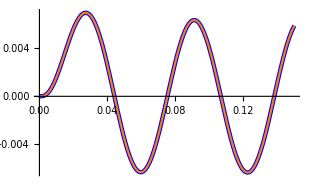

```mathematica
Show[plot4a,plot4b](*Son la misma funcion*)
```

### Pregunta 6

```mathematica
Clear[y]
```

```mathematica
RSolve[{y[n+1]-16 y[n-1]==2^(2n+1),y[0]==0},y[n],n]
```

{{y[n]→-2^(-3+2 n) ((-1)^(2 n)+(-1)^(1+n)-2 n-8 C[1]+8 (-1)^n C[1])}}

### Pregunta 7

```mathematica
InverseZTransform[z((z^2+4z+1)/(z-1)^4),z,k]
```

k^3

```mathematica
Limit[1/(3*2)*D[z^k(z^2+4z+1),{z,3}],z->1]
```

k^3

```mathematica
Residue[z^k(z^2+4z+1)/(z-1)^4,{z,1}]
```

k^3